```mathematica
FindEquationalProof[
poop[even,poop[even,odd]]==odd,
poop[even,odd]==odd
]
```

ProofObject[…]

```mathematica
FindEquationalProof[
ForAll[x,add[mult[odd,x],odd]==even],{
x==odd∨even,
mult[odd,even]==even,
mult[odd,even]==mult[even,odd],
mult[odd,odd]==odd,
mult[even,even]==even,
ForAll[x,mult[odd,x]==x],
ForAll[x,mult[even,x]==even]
}]
```

FindEquationalProof::invs: Invalid specification of propositions ∀_x add[mult[odd,x],odd]==even and axioms {x==odd||even,mult[odd,even]==even,mult[odd,even]==mult[even,odd],mult[odd,odd]==odd,mult[even,even]==even,∀_x mult[odd,x]==x,∀_x mult[even,x]==even}.

FindEquationalProof[∀_x add[mult[odd,x],odd]==even,{x==odd||even,mult[odd,even]==even,mult[odd,even]==mult[even,odd],mult[odd,odd]==odd,mult[even,even]==even,∀_x mult[odd,x]==x,∀_x mult[even,x]==even}]

```mathematica
FindEquationalProof[
ForAll[x,add[mult[odd,x],odd]==even],{
ForAll[x,mult[odd,x]==x],
ForAll[x,add[x,odd]==even]
}]
```

ProofObject[…]

```mathematica
FindEquationalProof[
poop[even,poop[even,poop[even,poop[even,poop[even,poop[even,odd]]]]]]==odd,
poop[even,odd]==odd
]
```

ProofObject[…]

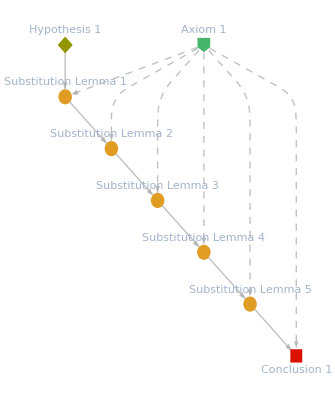

```mathematica
Out[10]["ProofGraph"]
```

```mathematica
FindEquationalProof[
ForAll[x,add[mult[even,x],odd]==even],{
ForAll[x,mult[even,x]==even],
add[even,odd]==even
}]
```

ProofObject[…]

```mathematica
FindEquationalProof[
lol,{
lol
}]
```

FindEquationalProof::invs: Invalid specification of propositions lol and axioms {lol}.

FindEquationalProof[lol,{lol}]

```mathematica
FindEquationalProof[
exist[lol]==true,{
not[exist[lol]]==false
}]
```

Failure[…]

```mathematica
FindEquationalProof[
not[exist[lol]],{
exist[lol]
}]
```

$Aborted

```mathematica
FindEquationalProof[
not[exist[lol]]==false,{
exist[lol]==true
}]
```

Failure[…]

```mathematica
FindEquationalProof[
ForAll[{a,b},not[or[a,b]]==and[not[a],not[b]]],{

}]
```

FindEquationalProof::invs: Invalid specification of propositions ∀_{a,b}not[or[a,b]]==and[not[a],not[b]] and axioms {}.

FindEquationalProof[∀_{a,b}not[or[a,b]]==and[not[a],not[b]],{}]

```mathematica
AxiomaticTheory[]
```

{AbelianGroupAxioms,AbelianHigmanNeumannAxioms,AbelianMcCuneAxioms,BooleanAxioms,GroupAxioms,HigmanNeumannAxioms,HillmanAxioms,HuntingtonAxioms,McCuneAxioms,MeredithAxioms,MonoidAxioms,RingAxioms,RobbinsAxioms,SemigroupAxioms,ShefferAxioms,WolframAlternateAxioms,WolframAxioms,WolframCommutativeAxioms}

```mathematica
AxiomaticTheory["BooleanAxioms"]
```

{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}

```mathematica
AxiomaticTheory["BooleanAxioms"][lol]
```

{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}[lol]

```mathematica
AxiomaticTheory["BooleanAxioms"][[lol]]
```

Part::pkspec1: The expression lol cannot be used as a part specification.

{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}⟦lol⟧

```mathematica
Map[
#[[lol]]&
,AxiomaticTheory["BooleanAxioms"]]
```

Part::pkspec1: The expression lol cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{(∀_{a,b}a⊗b==b⊗a)⟦lol⟧,(∀_{a,b}a⊕b==b⊕a)⟦lol⟧,(∀_{a,b}a⊗(b⊕b̄)==a)⟦lol⟧,(∀_{a,b}a⊕b⊗b̄==a)⟦lol⟧,(∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c)⟦lol⟧,(∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c))⟦lol⟧}

```mathematica
AxiomaticTheory["BooleanAxioms","Axioms"]
```

```mathematica
{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}
```

```mathematica
AxiomaticTheory["BooleanAxioms","Properties"]
```

{Axioms,EquivalentTheories,NotableTheorems,OperatorArities,Operators,Properties,Subtheories,Supertheories}

```mathematica
Grid@
Map[{#,AxiomaticTheory["BooleanAxioms",#]}&,AxiomaticTheory["BooleanAxioms","Properties"]
]
```

Axioms | {∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}
EquivalentTheories | {HuntingtonAxioms,RobbinsAxioms,ShefferAxioms,HillmanAxioms,MeredithAxioms,WolframAxioms,WolframAlternateAxioms,WolframCommutativeAxioms}
NotableTheorems | <|ImpliesHuntingtonAxioms→{∀_{a,b}a⊕b==b⊕a,∀_{a,b,c}a⊕(b⊕c)==(a⊕b)⊕c,∀_{a,b}OverBar[ā⊕b]⊕OverBar[ā⊕b̄]==a},ImpliesRobbinsAxioms→{∀_{a,b}a⊕b==b⊕a,∀_{a,b,c}a⊕(b⊕c)==(a⊕b)⊕c,∀_{a,b}OverBar[OverBar[a⊕b]⊕OverBar[a⊕b̄]]==a},DoubleNegation→{∀_a OverBar[ā]==a},DeMorgan→{∀_{a,b}OverBar[a⊕b]==ā⊗b̄,∀_{a,b}OverBar[a⊗b]==ā⊕b̄}|>
OperatorArities | {CircleTimes→2,CirclePlus→2,OverBar→1}
Operators | <|And→CircleTimes,Or→CirclePlus,Not→OverBar|>
Properties | {Axioms,EquivalentTheories,NotableTheorems,OperatorArities,Operators,Properties,Subtheories,Supertheories}
Subtheories | {}
Supertheories | {}

```mathematica
AxiomaticTheory["BooleanAxioms"]
```

{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}

```mathematica
FindEquationalProof[
∀_{a,b}OverBar[(a⊗b)]==(ā⊕b̄),
{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}
]
```

ProofObject[…]

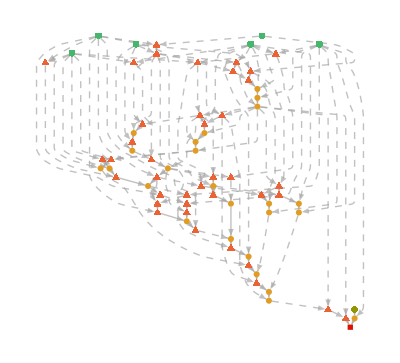

```mathematica
ProofObject[…]["ProofGraph"]
```

```mathematica
FindEquationalProof[
∀_{a,b}OverBar[(a⊗b)]==(ā⊕b̄),
{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}
]
```

```mathematica
FindEquationalProof[
ForAll[x,add[mult[odd,x],odd]==even],{
ForAll[x,mult[odd,x]==x],
ForAll[x,add[x,odd]==even]
}]
```

ProofObject[…]

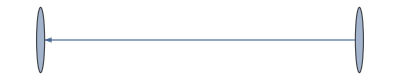

```mathematica
Graph[a->b]
```

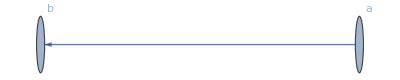

```mathematica
Show[SetProperty[Graph[{a, b}, {DirectedEdge[a, b]}],VertexLabels->"Name"],PlotRange->All]
```

```mathematica
Graph[{a, b}, {DirectedEdge[a, b]},VertexLabels->"Name",PlotRange->All]
```

-Graphics-

```mathematica
Graph[DirectedEdge[a, b],VertexLabels->"Name",PlotRange->All]
```

-Graphics-

```mathematica
Graph[a->b,VertexLabels->"Name",PlotRange->All]
```

-Graphics-

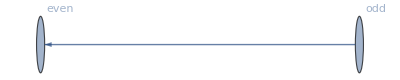

```mathematica
Graph[odd->even,VertexLabels->"Name",PlotRange->All]
```

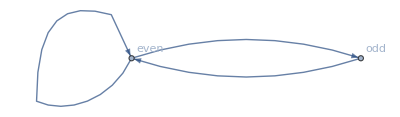

```mathematica
Graph[{
odd->even,
even->odd,
even->even
},VertexLabels->"Name",PlotRange->All]
```

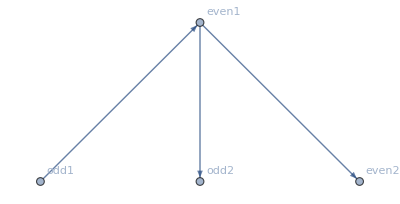

```mathematica
Graph[{
odd1->even1,
even1->odd2,
even1->even2
},VertexLabels->"Name",PlotRange->All]
```

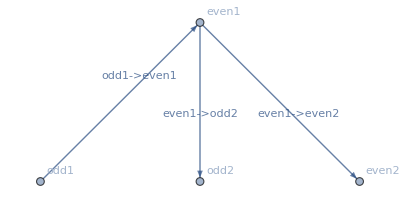

```mathematica
Show[SetProperty[Graph[{odd1, even1, odd2, even2}, {DirectedEdge[odd1, even1], DirectedEdge[even1, odd2], DirectedEdge[even1, even2]}, {PlotRange -> All, VertexLabels -> {"Name"}}],EdgeLabels->Placed["Name",1./GoldenRatio]],PlotRange->All]
```

```mathematica
Graph[{
odd1->even1,
even1->odd2,
even1->even2
},VertexLabels->"Name",PlotRange->All]
```

```mathematica
Graph[{
odd->even,
even->odd,
even->even
},{up,down,down},VertexLabels->"Name",PlotRange->All]
```

Graph[{odd→even,even→odd,even→even},{up,down,down},VertexLabels→Name,PlotRange→All]

```mathematica
Graph[{odd1, even1, odd2, even2}, {DirectedEdge[odd1, even1], DirectedEdge[even1, odd2], DirectedEdge[even1, even2]}, PlotRange -> All, VertexLabels -> {"Name"},EdgeLabels->Placed["Name",1./GoldenRatio],PlotRange->All]
```

-Graphics-

```mathematica
Graph[{
odd->even,
even->odd
},{up,down},VertexLabels->"Name",PlotRange->All]
```

Graph[{odd→even,even→odd},{up,down},VertexLabels→Name,PlotRange→All]

```mathematica
Graph[{
odd->even,
even->odd
},{up,down},VertexLabels->"Name"]
```

Graph[{odd→even,even→odd},{up,down},VertexLabels→Name]

```mathematica
Graph[{
odd1->even1,
even1->odd2,
even1->even2
},VertexLabels->"Name",PlotRange->All,EdgeLabels->Placed["Name",1./GoldenRatio]]
```

-Graphics-

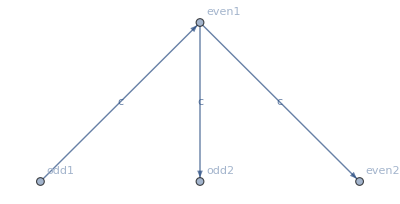

```mathematica
Graph[{
odd1->even1,
even1->odd2,
even1->even2
},VertexLabels->"Name",PlotRange->All,EdgeLabels->{a,b,c}]
```

```mathematica
arch[1]:=2
```

```mathematica
arch[4]:=4
```

```mathematica
arch[2]
```

arch[2]

```mathematica
arch[1]
```

2

```mathematica
arch[4]
```

4

```mathematica
Graph[{
odd1->even1,
even1->odd2,
even1->even2
},VertexLabels->"Name",
PlotRange->All,
EdgeLabels->{
odd1->even1->a,
even1->odd2->b,
even1->even2->c
}]
```

Graph[{odd1→even1,even1→odd2,even1→even2},VertexLabels→Name,PlotRange→All,EdgeLabels→{odd1→even1→a,even1→odd2→b,even1→even2→c}]

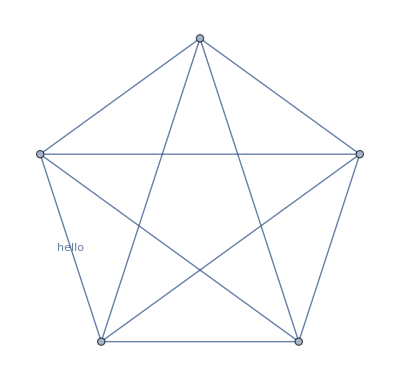

```mathematica
CompleteGraph[5,EdgeLabels->{1<->2->"hello"}]
```

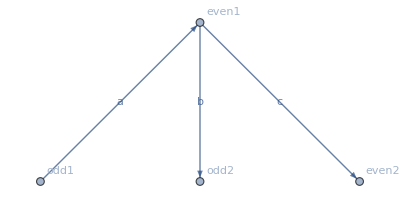

```mathematica
Graph[{
odd1->even1,
even1->odd2,
even1->even2
},VertexLabels->"Name",
PlotRange->All,
EdgeLabels->{
(odd1->even1)->a,
(even1->odd2)->b,
(even1->even2)->c
}]
```

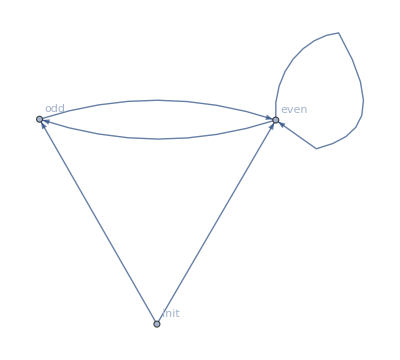

```mathematica
Graph[{
init->even,
init->odd,
even->odd,
even->even,
odd->even
},VertexLabels->"Name",
PlotRange->All]
```

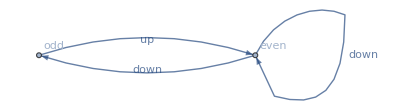

```mathematica
Graph[{
even->odd,
even->even,
odd->even
},VertexLabels->"Name",
PlotRange->All,
EdgeLabels->{
(even->odd)->down,
(even->even)->down,
(odd->even)->up
}]
```